#### Value function for intrinsic policy, v_int ; Variance of OU process ψ(s); Value function of OU policy, vOU; Total value function, vFull(s_c)

```mathematica
vint[ϕst_,ko_, s_, sc_]:=ϕst/ko(Exp[-ko s/ϕst]-Exp[-ko sc/ϕst])
ψ[s_,sc_,vo_,d_,ν_]:=(vo^2 d)/ν((2 ν (s-sc))/vo - Exp[-2ν(s-sc)/vo]+4Exp[-ν(s-sc)/vo]-3)+0.1
(*vOU[s_,sc_,vo_,d_,ν_, σ_, μ_]:= (2 σ μ)/ψ[s,sc,vo,d,ν]*)
vOU[s_,sc_,vo_,d_,ν_, σ_, μ_]:=NIntegrate[(2 μ √(σ^2-t^2))/ψ[s-t,sc,vo,d,ν],{t,0,σ}]
vFull[sSt_, sc_,vo_,d_,ν_, σ_, μ_,ϕst_,ko_] := vint[ϕst,ko, 0, sc]+vOU[sSt,sc,vo,d,ν, σ, μ]
```

Evolution of value function of intrinsic policy

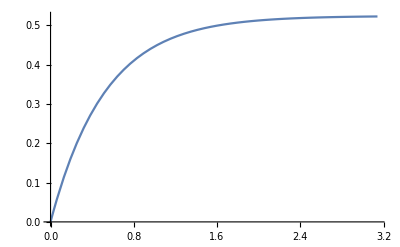

```mathematica
Plot[vint[π/6,1,0,sc],{sc,0,π},PlotRange->Automatic]
```

Evolution of variance of OU process

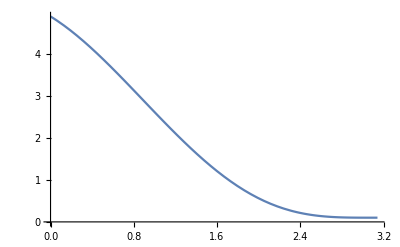

```mathematica
Plot[ψ[sc+2Cos[sc/2],sc,1,(π-sc),1],{sc,0,π},PlotRange->Automatic]
```

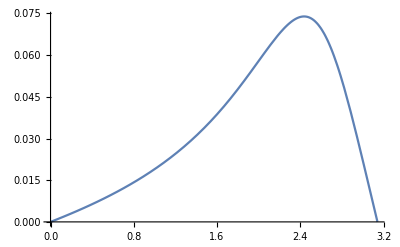

```mathematica
(*vOU[s_,sc_,vo_,d_,ν_, σ_, μ_]*)
Plot[vOU[π,sc,1,sc^-1,1, 0.1,( π-sc)],{sc,0,π},PlotRange->Automatic]
```

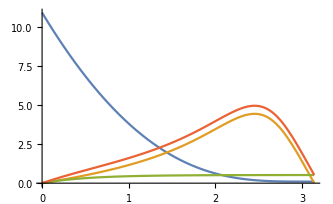

plot.pdf

```mathematica
plt = Plot[{ψ[π,sc,1,π-sc,1],vOU[π,sc,1,sc^-1,1, 1, π-sc],vint[π/6,1,0,sc], vOU[π,sc,1,sc^-1,1, 1, π-sc]+vint[π/6,1,0,sc]},{sc,0,π},PlotRange->Automatic]
(*Export["plot.pdf",plt]*)
```

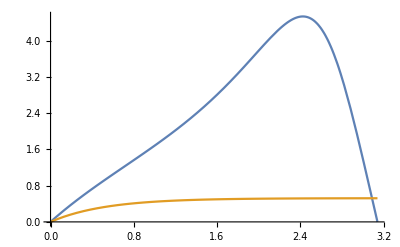

```mathematica
Plot[{vOU[sc+2Cos[sc/2],sc,1,sc^-1,1, 1,π-sc],vint[π/6,1,0,sc]},{sc,0,π},PlotRange->Automatic]
```

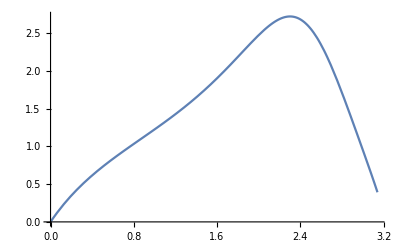

```mathematica
(*vFull[sSt_, sc_,vo_,d_,ν_, σ_, μ_,ϕst_,ko_] *)
Plot[vFull[sc+2 Cos[sc/2], sc,1,sc^-1,1,0.5,π-sc,π/8,1],{sc,0,π},PlotRange->Automatic]
```

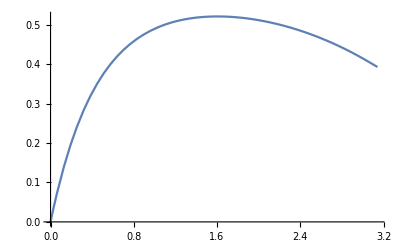

```mathematica
Plot[vFull[sc+2 Cos[sc/2], sc,0.5,0.1 sc^-1,10,0.1,π-sc,π/8,1],{sc,0,π},PlotRange->All]
```

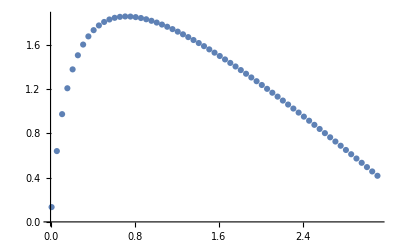

tabFull.csv

```mathematica
tabLst = Table[{sc,vFull[sc+2 Cos[sc/2], sc,0.5,0.01 sc^-1,10,0.1,5(π-sc),π/8,1]},{sc,0.01,π,0.05}];
ListPlot[tabLst]
Export["tabFull.csv",tabLst]
```

0.5

0.1

10

0.1

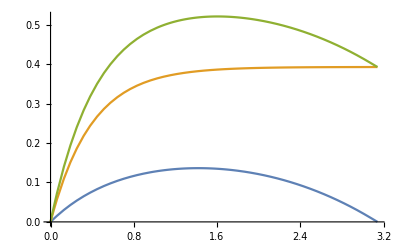

```mathematica
(*vOU[s_,sc_,vo_,d_,ν_, σ_, μ_]
vint[ϕst_,ko_, s_, sc_]
vFull[sSt_, sc_,vo_,d_,ν_, σ_, μ_,ϕst_,ko_]*)
voF = 0.5
dF = 0.1
νF = 10
σF = 0.1
Plot[{vOU[sc+2 Cos[sc/2],sc,voF,dF sc^-1,νF, σF, π-sc],vint[π/8,1,0,sc], vOU[sc+2 Cos[sc/2],sc,voF,dF sc^-1,νF, σF, π-sc]+vint[π/8,1,0,sc]},{sc,0,π},PlotRange->All]
```

#### Non-dimensional functional forms

Considering success within a circle of radius σ

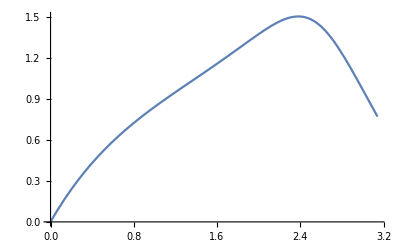

```mathematica
vintND[ϕst_,k_, s_, sc_]:=ϕst/k(Exp[-k s/ϕst]-Exp[-k sc/ϕst])
ψND[s_,sc_,pe_]:=pe(2  (s-sc) - Exp[-2(s-sc)]+4Exp[-(s-sc)]-3)+0.1
(*vOUND[s_,sc_,pe_, σ_, μ_]:= (2 σ μ)/ψND[s,sc,pe]*)
vOUND[s_,sc_,pe_, σ_, μ_]:=NIntegrate[(2 μ √(σ^2-t^2))/ψND[s-t,sc,pe],{t,0,σ}]
vFullND[sSt_, sc_,pe_, σ_, μ_,ϕst_,k_] := vintND[ϕst,k, 0, sc]+vOUND[sSt,sc,pe, σ, μ]
(*Plot[vFullND[sc+2 Cos[sc/2], sc,sc^-1,(2 Cos[sc/2])/1,π-sc,π/4,1],{sc,0,π},PlotRange->Automatic]*)
Plot[vFullND[sc+2 Cos[sc/2], sc,sc^-1,0.3,π-sc,π/4,1],{sc,0,π},PlotRange->Automatic]
```

Considering success as intersecting a line of width σ/2

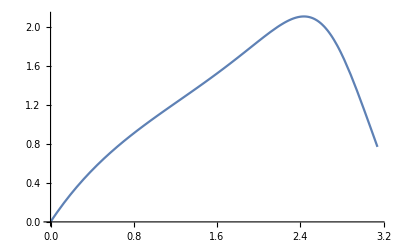

```mathematica
vintND[ϕst_,k_, s_, sc_]:=ϕst/k(Exp[-k s/ϕst]-Exp[-k sc/ϕst])
ψND[s_,sc_,pe_]:=pe(2  (s-sc) - Exp[-2(s-sc)]+4Exp[-(s-sc)]-3)+0.1
vOUND[s_,sc_,pe_, σ_, μ_]:= (σ μ)/ψND[s,sc,pe]
vFullND[sSt_, sc_,pe_, σ_, μ_,ϕst_,k_] := vintND[ϕst,k, 0, sc]+vOUND[sSt,sc,pe, σ, μ]
(*Plot[vFullND[sc+2 Cos[sc/2], sc,sc^-1,(2 Cos[sc/2])/1,π-sc,π/4,1],{sc,0,π},PlotRange->Automatic]*)
Plot[vFullND[sc+2 Cos[sc/2], sc,sc^-1,0.3,π-sc,π/4,1],{sc,0,π},PlotRange->Automatic]
```

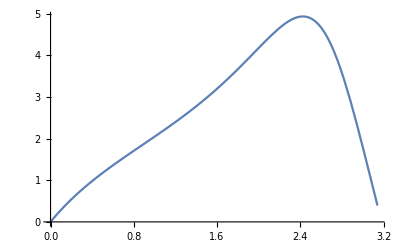

```mathematica
Plot[vFullND[sc+2 Cos[sc/2], sc,sc^-1,1,π-sc,π/8,1],{sc,0,π},PlotRange->Automatic]
```

1/2

0.1

10

0.01

1/20

2.

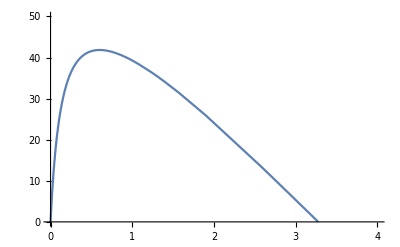

```mathematica
voF = (5 10^-3)/10^-2
dF = 0.1
νF = 10
peF =dF/νF
lν = voF/νF
σF = 0.1/lν
 Plot[vFullND[sc+2 Cos[sc/2], sc,peF sc^-1,σF,π-sc,π/8,1 lν],{sc,0,π /lν},PlotRange->{{0,4},{0,50}}]
```

```mathematica
Plot[vFullND[sc+2 Cos[sc/2], sc,sc^-1,0.3,π-sc,π/4,1],{sc,0,π},PlotRange->Automatic]
```

```mathematica
Integrate[Exp[-s/ϕs],{s,0,s}]
```

ϕs-ⅇ^(-s/ϕs) ϕs

```mathematica
DSolve[{x'[t]==-2 α x[t] + 2d, x[0]==0},x[t],t]
```

{{x[t]→(d ⅇ^(-2 t α) (-1+ⅇ^(2 t α)))/α}}

```mathematica
ψND[s,sc,pe]
```

0.1+pe (-3-ⅇ^(-2 (s-sc))+4 ⅇ^(-s+sc)+2 (s-sc))

```mathematica
Integrate[(μ √(σ^2-t^2))/(ψND[sFin-t,sc,pe]-0.1),{t,0.01,σ}]
```

∫_0.01^σ (μ √(-t^2+σ^2))/(0.+pe (-3-ⅇ^(-2 (-sc+sFin-t))+4 ⅇ^(sc-sFin+t)+2 (-sc+sFin-t)))ⅆt

```mathematica
ψND[sSt,sc,pe]
```

0.1+pe (-3+4 ⅇ^(sc-sSt)-ⅇ^(-2 (-sc+sSt))+2 (-sc+sSt))